## Loop

```mathematica
Loop:=(For[


Array[AlleleFreqA,Nloci];
Do[AlleleFreqA[i]={},{i,1,Nloci}];
TotalLoadA={};

AUC1A=IntroFreq2;
AUC2A=IntroFreqTotal;
AUC3A=IntroFreqTotal;
AUC4A=0;
AUC5A=0;

DiploidFitnessTable=Table[1,{i,NHaplotypes},{j,NHaplotypes}];

Do[
If[BitGet[BitOr[i-1,j-1],1]-BitGet[BitOr[i-1,j-1],2]== 0,DiploidFitnessTable[[i,j]]*=1,DiploidFitnessTable[[i,j]]*=tox];
If[BitGet[i-1,1]+BitGet[j-1,1]==1,DiploidFitnessTable[[i,j]]*=(1-sc)^(1/2),If[BitGet[i-1,1]+BitGet[j-1,1]==2,DiploidFitnessTable[[i,j]]*=(1-sc),DiploidFitnessTable[[i,j]]*=1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];


Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,0]+BitGet[j-1,0]==1,DiploidFitnessTable[[i,j]]*=h1]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,3]+BitGet[j-1,3]==1,DiploidFitnessTable[[i,j]]*=h2]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,1]+BitGet[j-1,1])>0,
If[BitGet[i-1,4]+BitGet[j-1,4]==1,DiploidFitnessTable[[i,j]]*=h3]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

MaleViabilitySelection=DiploidFitnessTable;

FemaleViabilitySelection=DiploidFitnessTable;
Do[
If[(BitGet[i-1,0]+BitGet[j-1,0])==1,FemaleViabilitySelection[[i,j]]*=(1-sp1)^(1/2),
If[(BitGet[i-1,0]+BitGet[j-1,0])==2,FemaleViabilitySelection[[i,j]]*=(1-sp1)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,3]+BitGet[j-1,3])==1,FemaleViabilitySelection[[i,j]]*=(1-sp2)^(1/2),
If[(BitGet[i-1,3]+BitGet[j-1,3])==2,FemaleViabilitySelection[[i,j]]*=(1-sp2)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

Do[
If[(BitGet[i-1,4]+BitGet[j-1,4])==1,FemaleViabilitySelection[[i,j]]*=(1-sp3)^(1/2),
If[(BitGet[i-1,4]+BitGet[j-1,4])==2,FemaleViabilitySelection[[i,j]]*=(1-sp3)]],
{i,1,NHaplotypes},{j,1,NHaplotypes}];

MaskProb=Function[{mask,Nloci},
For[prob=1.0;z=1, z<Nloci,z++,
If[BitGet[mask,(Nloci-z)]==BitGet[mask,(Nloci-z-1)],
prob*=(1-recrate[z]),
prob*=recrate[z]]]];

ZygoteGenotypes=Function[{i,j,mask},
For[zyg1=0;zyg2=0;k=0,k<Nloci,k++,
If[BitGet[mask,k]==0,
zyg1=BitOr[zyg1,(BitAnd[i,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[j,(2^k)])],
zyg1=BitOr[zyg1,(BitAnd[j,(2^k)])];zyg2=BitOr[zyg2,(BitAnd[i,(2^k)])]]]];

RecTable=Table[0,{i,NHaplotypes},{j,NHaplotypes},{k,NHaplotypes}];
For[i=0,i<NHaplotypes,i++,
For[j=0,j<NHaplotypes,j++,
For[mask=0,mask<masklim,mask++,
MaskProb[mask,Nloci];
zygoteProb =0.5*prob;
ZygoteGenotypes[i,j,mask];
RecTable[[(i+1),(j+1),(zyg1+1)]]+=zygoteProb;
RecTable[[(i+1),(j+1),(zyg2+1)]]+=zygoteProb;]]];

g=0,g<Generations+1,g++,

MaleGenoFreqSelecA=MaleGenoFreqA*MaleViabilitySelection/Total[MaleGenoFreqA*MaleViabilitySelection,2];
FemaleGenoFreqSelecA=FemaleGenoFreqA*FemaleViabilitySelection/Total[FemaleGenoFreqA*FemaleViabilitySelection,2];

TotalLoadt1A=1-Total[FemaleGenoFreqA*FemaleViabilitySelection,2];

If[g==0,
MaleGenoFreqSelecA[[1,1]]=1-IntroFreq1-IntroFreq2;
MaleGenoFreqSelecA[[7,7]]=IntroFreq1;
MaleGenoFreqSelecA[[8,8]]=IntroFreq2;
MaleGenoFreqSelecA=MaleGenoFreqSelecA/(Total[MaleGenoFreqSelecA,2]);

FemaleGenoFreqSelecA[[1,1]]=1-IntroFreq1-IntroFreq2;
FemaleGenoFreqSelecA[[7,7]]=IntroFreq1;
FemaleGenoFreqSelecA[[8,8]]=IntroFreq2;
FemaleGenoFreqSelecA=FemaleGenoFreqSelecA/(Total[FemaleGenoFreqSelecA,2])];


If[g==thresh2,
MaleGenoFreqSelecA*=(1-IntroFreq3);
MaleGenoFreqSelecA[[16,16]]+=IntroFreq3;
MaleGenoFreqSelecA=MaleGenoFreqSelecA/(Total[MaleGenoFreqSelecA,2]);

FemaleGenoFreqSelecA*=(1-IntroFreq3);
FemaleGenoFreqSelecA[[16,16]]+=IntroFreq3;
FemaleGenoFreqSelecA=FemaleGenoFreqSelecA/(Total[FemaleGenoFreqSelecA,2])];

If[g==thresh3,
MaleGenoFreqSelecA*=(1-IntroFreq4);
MaleGenoFreqSelecA[[NHaplotypes,NHaplotypes]]+=IntroFreq4;
MaleGenoFreqSelecA=MaleGenoFreqSelecA/(Total[MaleGenoFreqSelecA,2]);

FemaleGenoFreqSelecA*=(1-IntroFreq4);
FemaleGenoFreqSelecA[[NHaplotypes,NHaplotypes]]+=IntroFreq4;
FemaleGenoFreqSelecA=FemaleGenoFreqSelecA/(Total[FemaleGenoFreqSelecA,2])];


Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
MaleGenoFreqSelecA[[k+1,l+1]]+=MaleGenoFreqSelecA[[i+1,j+1]];MaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,3]+BitGet[j,3])==1,k=BitSet[k,3];l=BitSet[l,3];
MaleGenoFreqSelecA[[k+1,l+1]]+=MaleGenoFreqSelecA[[i+1,j+1]];MaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,4]+BitGet[j,4])==1,k=BitSet[k,4];l=BitSet[l,4];
MaleGenoFreqSelecA[[k+1,l+1]]+=MaleGenoFreqSelecA[[i+1,j+1]];MaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];


Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,0]+BitGet[j,0])==1,k=BitSet[k,0];l=BitSet[l,0];
FemaleGenoFreqSelecA[[k+1,l+1]]+=FemaleGenoFreqSelecA[[i+1,j+1]];FemaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,3]+BitGet[j,3])==1,k=BitSet[k,3];l=BitSet[l,3];
FemaleGenoFreqSelecA[[k+1,l+1]]+=FemaleGenoFreqSelecA[[i+1,j+1]];FemaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

Do[k=i;l=j;If [BitGet[BitOr[i,j],1]==1,If[(BitGet[i,4]+BitGet[j,4])==1,k=BitSet[k,4];l=BitSet[l,4];
FemaleGenoFreqSelecA[[k+1,l+1]]+=FemaleGenoFreqSelecA[[i+1,j+1]];FemaleGenoFreqSelecA[[i+1,j+1]]=0;
]],{i,0,NHaplotypes-1},{j,0,NHaplotypes-1}];

SpermTable=RecTable*MaleGenoFreqSelecA;
EggTable=RecTable*FemaleGenoFreqSelecA;

SpermFreqt1A=Total[SpermTable,2];
EggFreqt1A=Total[EggTable,2];

SpermFreqA=SpermFreqt1A/(Total[SpermFreqt1A]);
EggFreqA=EggFreqt1A/(Total[EggFreqt1A]);

MaleGenoFreqT1A=KroneckerProduct[SpermFreqA,EggFreqA];
FemaleGenoFreqT1A=KroneckerProduct[SpermFreqA,EggFreqA];

MaleGenoFreqA=MaleGenoFreqT1A;
FemaleGenoFreqA=FemaleGenoFreqT1A;

Do[SpermAlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,SpermAlleleFreqT1A[i]+=SpermFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[EggAlleleFreqT1A[i]=0,{i,1,Nloci}];
Do[If[BitGet[j-1,i-1]==1,EggAlleleFreqT1A[i]+=EggFreqA[[j]]],{i,1,Nloci},{j,1,NHaplotypes}];

Do[AlleleFreqT1A[i]=(SpermAlleleFreqT1A[i]+EggAlleleFreqT1A[i])/2,{i,1,Nloci}];

AppendTo[AlleleFreqA[1],AlleleFreqT1A[1]];
AppendTo[AlleleFreqA[2],AlleleFreqT1A[2]];
AppendTo[AlleleFreqA[3],AlleleFreqT1A[3]];

If[g<thresh2,AppendTo[AlleleFreqA[4],Null],AppendTo[AlleleFreqA[4],AlleleFreqT1A[4]]];
If[g<thresh3,AppendTo[AlleleFreqA[5],Null],AppendTo[AlleleFreqA[5],AlleleFreqT1A[5]]];

AUC1A+=AlleleFreqT1A[1];
AUC2A+=AlleleFreqT1A[2];
AUC3A+=AlleleFreqT1A[3];
AUC4A+=AlleleFreqT1A[4];
AUC5A+=AlleleFreqT1A[5];
AppendTo[TotalLoadA,TotalLoadt1A];

])
```

## Multiple payload release

```mathematica
Nloci=5;
NGenotypes=3^Nloci;
NHaplotypes=2^Nloci;
recrate[1]=0.5; 
recrate[2]=0.5;
recrate[3]=0.5;
recrate[4]=0.5;
masklim=2^(Nloci-1);
tox=0;(*this describes the level of toxicity for the underdominance toxins. 1 is no effect on fitness, 0 is complete lethality *)

thresh2=20; (*this is the delay, in # of generations, for the 2nd introduction*)
thresh3=40; (*this is the delay, in # of generations, for the 3rd introduction*)

Generations=100;
h1=.95;
h2=.95;
h3=.95;
sc=0.05;

sp1=.5;
sp2=.5;
sp3=.5;

IntroFreqTotal=0.4;
IntroFreq2=0.01;
IntroFreq3=0.01;
IntroFreq4=0.01;
IntroFreq1=IntroFreqTotal-IntroFreq2;

MaleGenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
MaleGenoFreqA[[1,1]]=1;
FemaleGenoFreqA=Table[0,{i,1,NHaplotypes},{j,1,NHaplotypes}];
FemaleGenoFreqA[[1,1]]=1;
```

```mathematica
Loop;
```

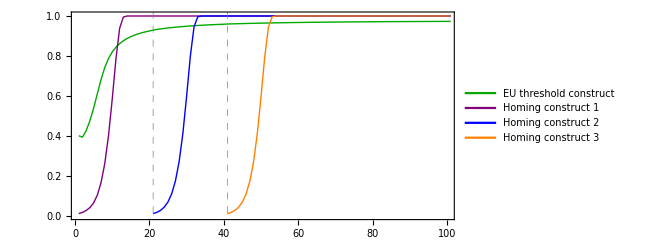

```mathematica
Fig3=ListPlot[{AlleleFreqA[2],AlleleFreqA[1],AlleleFreqA[4],AlleleFreqA[5]},
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,True,True},PlotStyle->{Directive[Darker[Green], Thick],Directive[Purple, Thick],Directive[Blue,Thick],Directive[Orange,Thick]},FrameStyle->Directive[20,Black],ImageSize->{480,260},
GridLines->{{thresh2+1,thresh3+1}},GridLinesStyle->Directive[Gray,Thick,Dashed],PlotLegends->Placed[LineLegend[{"EU threshold construct","Homing construct 1","Homing construct 2","Homing construct 3"},LegendMarkerSize->{22,5}],{Right,Center}],LabelStyle->16,AspectRatio->1/2]
```

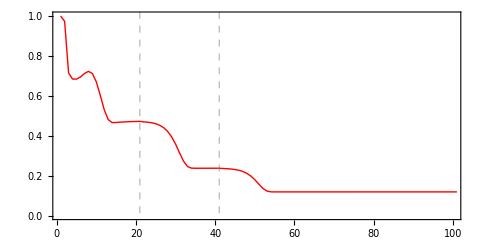

```mathematica
Fig4=ListPlot[{1-TotalLoadA},
PlotRange->{{1,Generations},{0,1.000000000000001}},Joined->True,Frame->{True,True,True,True},PlotStyle->{Directive[Red, Thick]},FrameStyle->Directive[20,Black],ImageSize->{480,260},
GridLines->{{thresh2+1,thresh3+1}},GridLinesStyle->Directive[Gray,Thick,Dashed],LabelStyle->14,AspectRatio->1/2]
```

## Combined Figure

```mathematica
CombinedFig=Grid[{{Column[{Style[Rotate["            Construct Frequency",90Degree],FontSize->18,FontFamily->"Helvetica"],Style[Rotate["   Mean population fitness      ",90Degree],FontSize->18,FontFamily->"Helvetica"],Null},ItemSize->Full],

Column[{Style["Driving multiple cargoes to reduce female fitness",FontSize->22,FontFamily->"Helvetica"],Fig3,Fig4,Style["                                        Generations",FontSize->18,FontFamily->"Helvetica"]},ItemSize->Full]}},Spacings->{0.5,2},Background->GrayLevel[.9]]
```

Construct Frequency
   Mean population fitness      
 | Driving multiple cargoes to reduce female fitness
-Graphics-
-Graphics-
                                        Generations